# Genetic programming

## Expression representation

```mathematica
GetLabelName[label_]:=Replace[label,Framed[Style[labelName_,___],___]:>labelName];

FunctionToGraph[expr_]:=Block[{tree,labels,functionNames,terminalNames,replaceRules,vertexLabels,order,pos},
tree = ToExpression@ToBoxes@TreeForm[expr];
labels=Cases[tree,Inset[name_,n_]:>Rule[n,GetLabelName[name]],Infinity] /.HoldForm[f_]:>f;
functionNames = DeleteDuplicates@Cases[expr,f_[_,_]:>f,All];
terminalNames = Complement[DeleteDuplicates[labels[[All,2]]],functionNames];
replaceRules = Join[Thread[functionNames->Map[Func,functionNames]], Thread[terminalNames->Map[Term,terminalNames]]];
vertexLabels = MapAt[ReplaceAll[#,replaceRules]&,labels,{All,2}];

{order,pos}=Catenate/@Cases[tree,Line[order_]|GraphicsComplex[pos_,___]:>{order,pos},Infinity];
{Graph[DirectedEdge@@@order,VertexLabels->labels],vertexLabels}
];
GraphToFunction[edgeList_,vertexLabels_]:=Block[{depthFirstScan},
depthFirstScan = Reverse@First@Last@Reap@DepthFirstScan[edgeList,1,{"PostvisitVertex"->(Sow[#]&)}] /. vertexLabels;

First@FixedPoint[SequenceReplace[#,{Func[f_],Term[y_],Term[x_]}:>Term[f[x,y]]]&,depthFirstScan]/.Term[x_]:>x
];
```

```mathematica
FullForm[x^4+y^3+2x+1]
```

Plus[1,Times[2,x],Power[x,4],Power[y,3]]

```mathematica
PlusFunc[1,PlusFunc[PlusFunc[TimesFunc[2,x],PowerFunc[x,4]],PowerFunc[y,3]]]
```

PlusFunc[1,PlusFunc[PlusFunc[TimesFunc[2,x],PowerFunc[x,4]],PowerFunc[y,3]]]

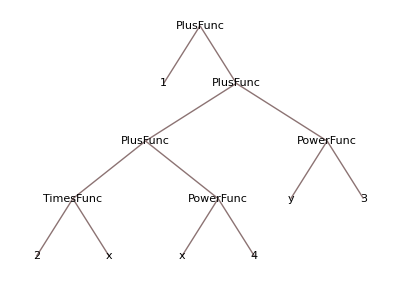

```mathematica
TreeForm[PlusFunc[1,PlusFunc[PlusFunc[TimesFunc[2,x],PowerFunc[x,4]],PowerFunc[y,3]]]]
```

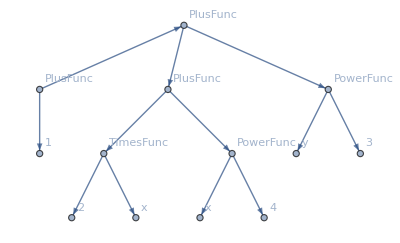
{-Graphics-,{1→Func[PlusFunc],2→Term[1],3→Func[PlusFunc],4→Func[PlusFunc],5→Func[TimesFunc],6→Term[2],7→Term[x],8→Func[PowerFunc],9→Term[x],10→Term[4],11→Func[PowerFunc],12→Term[y],13→Term[3]}}

```mathematica
FunctionToGraph[PlusFunc[1,PlusFunc[PlusFunc[TimesFunc[2,x],PowerFunc[x,4]],PowerFunc[y,3]]]]
```

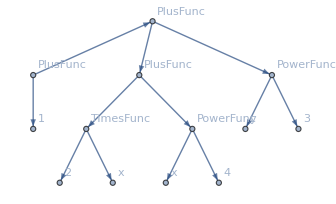
```mathematica
GraphToFunction[
-Graphics-,
{1->Func[PlusFunc],2->Term[1],3->Func[PlusFunc],4->Func[PlusFunc],5->Func[TimesFunc],6->Term[2],7->Term[x],8->Func[PowerFunc],9->Term[x],10->Term[4],11->Func[PowerFunc],12->Term[y],13->Term[3]}
]
```

PlusFunc[1,PlusFunc[PlusFunc[TimesFunc[2,x],PowerFunc[x,4]],PowerFunc[y,3]]]

## Operations on trees

```mathematica
Subtree[graph_,labels_,vertex_]:=Block[{children,toDelete,subtree,sublabels},
children = First@Last@Reap@DepthFirstScan[graph,vertex,{"PrevisitVertex"->(Sow[#]&)}];
toDelete = Complement[VertexList[graph],children];
subtree = VertexDelete[graph,Complement[VertexList[graph],children]];
sublabels = Cases[labels,x_/;MemberQ[children,First[x]]];

{subtree,sublabels}
];
FormatLabels[labels_]:=ReplaceAll[labels,{Term[x_]:>x,Func[x_]:>x}];
DeleteSubtree[graph_,labels_,vertex_]:=Block[{subtree,sublabels,subVertexes,conectionRemoved,withoutSubtree,newLabels},
{subtree,sublabels} = Subtree[graph, labels, vertex];
subVertexes = VertexList[subtree];
conectionRemoved = ReplaceAll[EdgeList[graph],((x_/;!MemberQ[subVertexes,x])->(y_/;MemberQ[subVertexes,y])):>x->Empty];
withoutSubtree = If[Length[Intersection[VertexList[conectionRemoved],subVertexes]]≠ 0,
VertexDelete[conectionRemoved,subVertexes],
conectionRemoved
];
newLabels = Complement[labels,sublabels];

{Graph[withoutSubtree,VertexLabels->FormatLabels[newLabels]],newLabels}
];
InsertSubtree[graph_,labels_,subtree_,sublabels_,subtreeRoot_]:=Block[{edges,missing,missingRules,newRules,insertionRules,formattedSubtree,formattedSublabels,formattedSubtreeRoot,newTree,newLabels},
If[!MemberQ[VertexList[graph],Empty],Return[$Failed]];

edges = DeleteCases[VertexList[graph],Empty];
missing = Complement[Range[Max[edges]],edges];
missingRules = Thread[Take[VertexList[subtree],UpTo[Length[missing]]]->Take[missing,UpTo[Length[VertexList[subtree]]]]];
If[Length[VertexList[subtree]]-Length[missing]>0,
newRules = Thread[Drop[VertexList[subtree],Length[missing]]-> Range[Max[edges]+1,Max[edges]+Length[VertexList[subtree]]-Length[missing]]];
insertionRules = Join[missingRules,newRules];
,
insertionRules = missingRules;
];

formattedSubtree = EdgeList[subtree]/.insertionRules;
formattedSublabels = MapAt[ReplaceAll[#,insertionRules]&,sublabels,{All,1}];
formattedSubtreeRoot = subtreeRoot /.insertionRules;
newTree = ReplaceAll[Join[EdgeList[graph],formattedSubtree],Empty->formattedSubtreeRoot];
newLabels = SortBy[Join[labels,formattedSublabels],First];

{Graph[newTree,VertexLabels->FormatLabels[newLabels]],newLabels}
];
```

```mathematica
f1 = LogicOr[LogicAnd[s1,LogicOr[LogicAnd[i3,s2],LogicAnd[i4,s2]]],LogicAnd[s1,LogicOr[LogicAnd[i1,s2],LogicAnd[i2,s2]]]];
f2 = LogicOr[LogicAnd[s1,LogicOr[LogicOr[i3,s2],LogicAnd[i4,s2]]],LogicXor[s1,s2]];
```

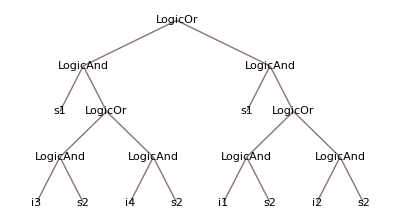
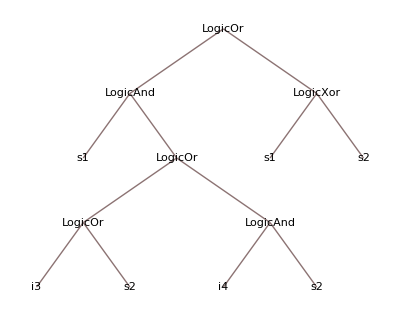

```mathematica
Map[TreeForm,{f1,f2}]
```

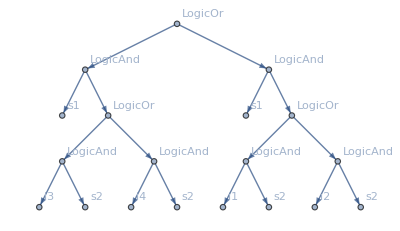
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
{g1,l1} = FunctionToGraph[f1]
```

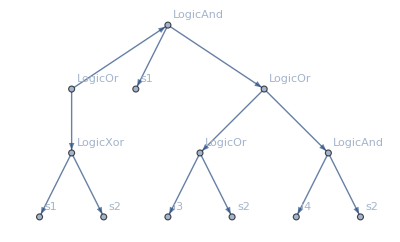
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicOr],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2]}}

```mathematica
{g2,l2} = FunctionToGraph[f2]
```

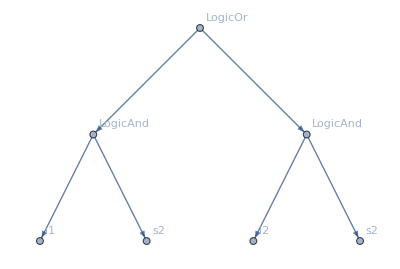
{-Graphics-,{13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
{sg1,sl1} = Subtree[g1,l1,13]
```

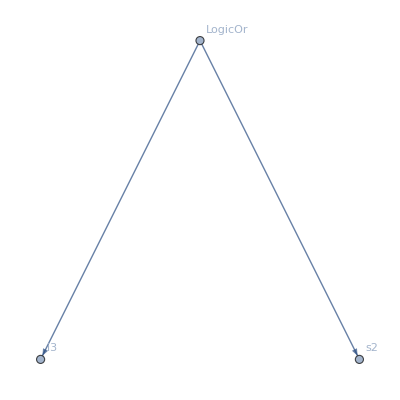
{-Graphics-,{5→Func[LogicOr],6→Term[i3],7→Term[s2]}}

```mathematica
{sg2,sl2} = Subtree[g2,l2,5]
```

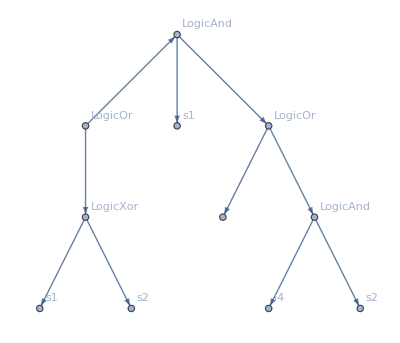
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2]}}

```mathematica
{dst,dl} = DeleteSubtree[g2,l2,5]
```

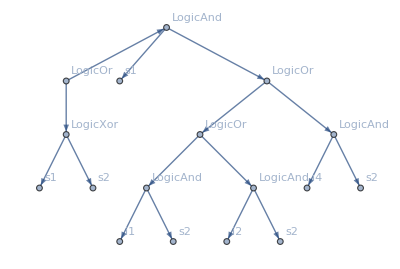
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicOr],6→Func[LogicAnd],7→Func[LogicAnd],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2],14→Term[i1],15→Term[s2],16→Term[i2],17→Term[s2]}}

```mathematica
InsertSubtree[dst,dl,sg1,sl1,13]
```

```mathematica
Apply[GraphToFunction,InsertSubtree[dst,dl,sg1,sl1,13]]
```

LogicOr[LogicAnd[s1,LogicOr[LogicOr[LogicAnd[i1,s2],LogicAnd[i2,s2]],LogicAnd[i4,s2]]],LogicXor[s1,s2]]

## Crossover

```mathematica
Crossover[graph1_,labels1_,graph2_,labels2_]:=Block[{vertex1,vertex2,cropped,sub},
vertex1 = RandomChoice[Drop[VertexList[graph1],1]];
vertex2 = RandomChoice[VertexList[graph2]];
cropped = DeleteSubtree[graph1,labels1,vertex1];
sub = Subtree[graph2,labels2,vertex2];

InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub],vertex2]
];
PopulationCrossover[population_,childrenPerCouple_]:=Block[{parts},
parts = Partition[RandomSample[population],2];
Apply[Join,Table[Map[Apply[Crossover,Flatten[#,1]]&,parts],childrenPerCouple]]
];
```

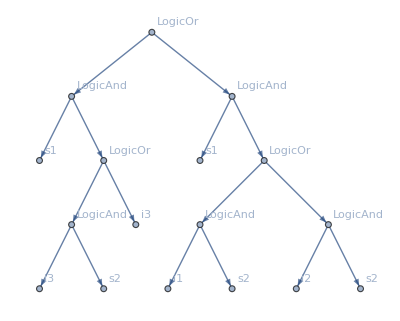
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Term[i3],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
Crossover[g1,l1,g2,l2]
```

## Mutation

```mathematica
TreeMutation[graph_,labels_]:=Block[{vertex1,vertex2,cropped,sub},
{vertex1,vertex2} = RandomSample[Drop[VertexList[graph],1],2];
cropped = DeleteSubtree[graph,labels,vertex1];
sub = Subtree[graph,labels,vertex2];

InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub],vertex2]
];
TerminalMutation[labels_,terminalSet_]:=Block[{replacePos,availableTerminals},
replacePos = RandomChoice[Cases[labels,(x_->_Term):>x]];
availableTerminals = Complement[terminalSet,Cases[labels,(replacePos->t_):>t]];

ReplaceAll[labels, (replacePos->_)->(replacePos->RandomChoice[availableTerminals])]
];
FunctionMutation[labels_,functionSet_]:=Block[{replacePos,availableFunctions},
replacePos = RandomChoice[Cases[labels,(x_->_Func):>x]];
availableFunctions = Complement[functionSet,Cases[labels,(replacePos->t_):>t]];

ReplaceAll[labels, (replacePos->_)->(replacePos->RandomChoice[availableFunctions])]
];
SymbolMutation[labels_,terminalSet_,functionSet_]:=FunctionMutation[TerminalMutation[labels,terminalSet],functionSet];
Mutation[graph_,labels_,terminalSet_,functionSet_]:=If[RandomReal[]≥0.5,TreeMutation[graph,labels],{graph,SymbolMutation[labels,terminalSet,functionSet]}];
PopulationMutate[population_,probability_,terminalSet_,functionSet_]:=Map[If[RandomReal[]<probability,Mutation[First[#],Last[#],terminalSet,functionSet],#]&,population];
```

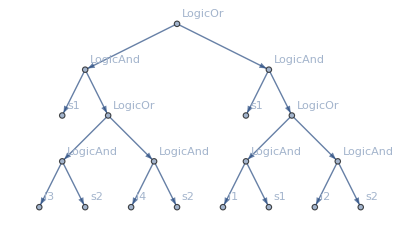
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s1],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
TreeMutation[g1,l1]
```

```mathematica
SymbolMutation[l1, {Term[s1],Term[s2],Term[i1],Term[i2],Term[i3],Term[i4]},{Func[LogicOr],Func[LogicAnd],Func[LogicXor]}]
```

{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicXor],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[i3]}

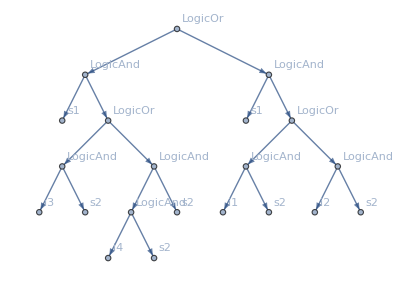
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Func[LogicAnd],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2],20→Term[i4],21→Term[s2]}}

```mathematica
Mutation[g1,l1, {Term[s1],Term[s2],Term[i1],Term[i2],Term[i3],Term[i4]},{Func[LogicOr],Func[LogicAnd],Func[LogicXor]}]
```

## Fitness function

```mathematica
EvaluateFunction[expr_,pts_,bloatControl_ : False]:=Block[{testInput,testFunctions,testResults,error},
testInput = Map[Thread[{x,y}->#]&,pts[[All,1;;2]]];
testFunctions = Map[expr/.#&,testInput];
testResults = Quiet[testFunctions/.{PlusFunc->Plus,TimesFunc->Times,PowerFunc->Power}];
error = Mean[Abs[testResults-pts[[All,3]]]];
If[error===Indeterminate, Return[0.0]];

Quiet@If[bloatControl,
N@(1/(1+error+0.01*LeafCount[expr])),

N@(1/(1+error))
]
];
EvaluatePopulation[population_,pts_,bloatControl_ : False]:=Block[{populationAsFunctions,scores},
populationAsFunctions = Map[Apply[GraphToFunction,#]&,population];
scores = Map[EvaluateFunction[#,pts,bloatControl]&,populationAsFunctions];

MapThread[<|"Genome"->#1,"Score"->#2|>&,{population,scores}]
];
```

```mathematica
pts = Flatten[Table[{x,y,1+x+x^4+y^3},{x,0,10},{y,0,10}],1];
```

```mathematica
EvaluateFunction[PowerFunc[x,0],pts]
```

0.

```mathematica
EvaluateFunction[PlusFunc[1,PlusFunc[PlusFunc[TimesFunc[2,x],PowerFunc[x,4]],PowerFunc[y,3]]],pts]
```

0.166667

```mathematica
EvaluateFunction[PlusFunc[1,PlusFunc[PlusFunc[TimesFunc[2,x],PowerFunc[x,4]],PowerFunc[y,3]]],pts,True]
```

0.163132

## Population initialization

```mathematica
GenerateSeed[terminalSet_,functionSet_]:=Block[{head,args,labels,graph},
head = RandomChoice[functionSet];
args = RandomSample[terminalSet,2];
labels = Thread[Range[3]->Join[{head},args]];
graph = Graph[{1->2,1->3},VertexLabels->FormatLabels[Thread[Range[3]->Join[{head},args]]]];

{graph,labels}
];
GenerateInitialPopulation[size_,terminalSet_,functionSet_,recombinations_,expectedOutput_]:=Block[{seeds,population},
seeds = Table[GenerateSeed[terminalSet,functionSet],size];
population = Nest[PopulationCrossover[#,2]&,seeds,recombinations];

EvaluatePopulation[population,expectedOutput]
];
```

```mathematica
terminalSet = {Term[x],Term[y],Term[1],Term[2],Term[3],Term[4]};
functionSet = {Func[PlusFunc],Func[TimesFunc],Func[PowerFunc]};
```

```mathematica
pts = Flatten[Table[{x,y,1+x+x^4+y^3},{x,0,10},{y,0,10}],1];
```

```mathematica
population = GenerateInitialPopulation[10,terminalSet,functionSet,0,pts];
```

## Selection

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateRankedSelection[evaluatedGenome_,n_]:= Part[Reverse@SortBy[evaluatedGenome,Key["Score"]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]]
```

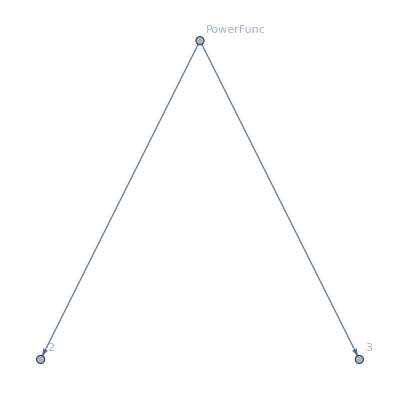
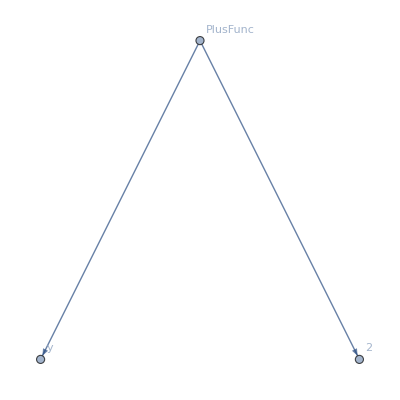
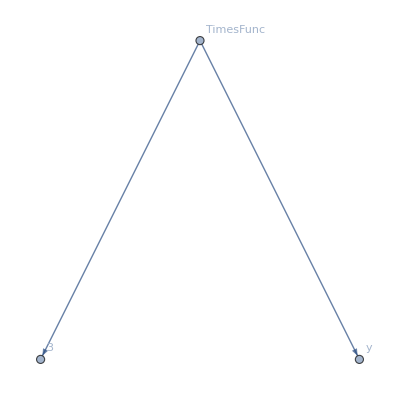
{<|Genome→{-Graphics-,{1→Func[PowerFunc],2→Term[2],3→Term[3]}},Score→0.000387993|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Term[y],3→Term[2]}},Score→0.000387893|>,<|Genome→{-Graphics-,{1→Func[TimesFunc],2→Term[3],3→Term[y]}},Score→0.000389103|>}

```mathematica
ProportionateRankedSelection[population,3]
```

## Main algorithm

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]]
```

```mathematica
Generation[population_,terminalSet_,functionSet_,survivors_,mutationProb_,pts_,bloatControl_]:=Block[{evaluated,fittest,newGeneration,mutated,childrenPerCouple},
fittest = ProportionateRankedSelection[population,survivors];
childrenPerCouple = (2 Length[population])/survivors;
newGeneration = PopulationCrossover[fittest[[All,"Genome"]],childrenPerCouple];
mutated = PopulationMutate[newGeneration,mutationProb,terminalSet,functionSet];

EvaluatePopulation[mutated,pts,bloatControl]
];
GeneticOptimize[population_,terminalSet_,functionSet_,survivors_,mutationProb_,pts_,bloatControl_,generations_]:=
ProgressNestList[
Generation[#,terminalSet,functionSet,survivors,mutationProb,pts,bloatControl]&,
population,generations,
"Label"->"Generation"
];
```

```mathematica
terminalSet = {Term[x],Term[y],Term[1],Term[2],Term[3],Term[4]};
functionSet = {Func[PlusFunc],Func[TimesFunc],Func[PowerFunc]};
```

```mathematica
pts = Flatten[Table[{x,y,1+2x+x^4+y^3},{x,0,10},{y,0,10}],1];
```

```mathematica
population = GenerateInitialPopulation[50,terminalSet,functionSet,0,pts];
```

```mathematica
optimization = GeneticOptimize[population,terminalSet, functionSet, 10,0.3,pts,True,20] ;
```

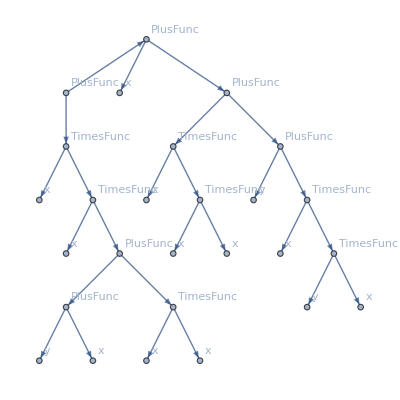
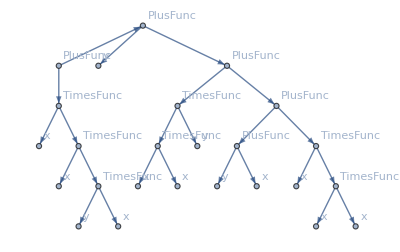
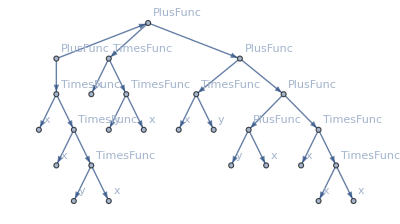
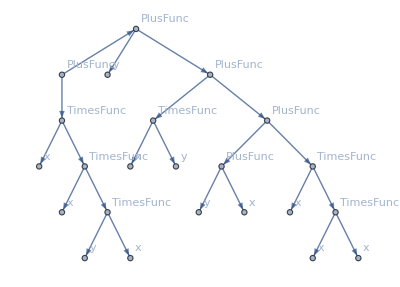
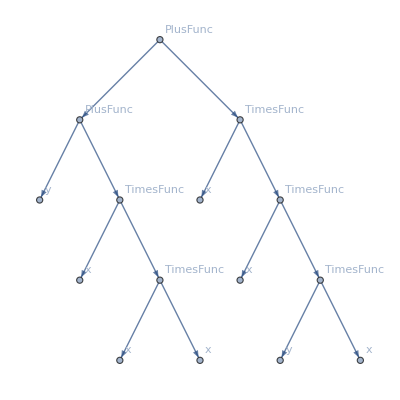
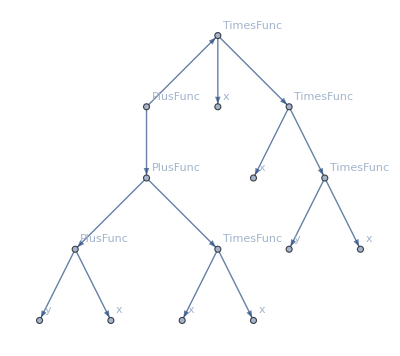
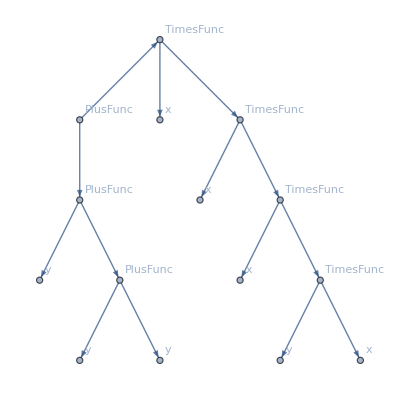
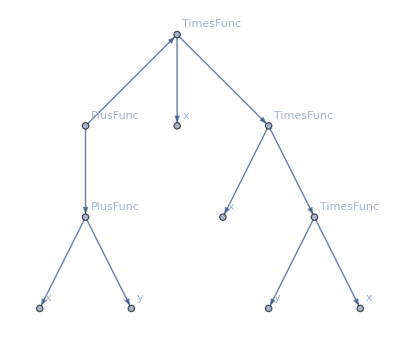
{<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[PlusFunc],10→Func[PlusFunc],11→Func[TimesFunc],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[4],15→Func[TimesFunc],16→Term[y],17→Func[PlusFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x],24→Term[x],25→Term[x],26→Term[y],27→Term[x]}},Score→0.00180825|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Func[TimesFunc],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x],24→Term[x],25→Term[x]}},Score→0.00105507|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[TimesFunc],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x],24→Term[x],25→Func[TimesFunc],26→Term[y],27→Term[x]}},Score→0.00105166|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x]}},Score→0.00103546|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[x],15→Term[x]}},Score→0.00102285|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[PlusFunc],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Term[x],14→Term[y],15→Term[x]}},Score→0.000852472|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[PlusFunc],4→Term[y],5→Func[PlusFunc],6→Term[3],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[x],11→Func[TimesFunc],12→Term[y],13→Term[y],14→Term[y],15→Term[x]}},Score→0.000834223|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000829163|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000829163|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[x],11→Term[x]}},Score→0.000829163|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000829163|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Term[x],3→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000825979|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[x],15→Term[x]}},Score→0.000742144|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[4],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[TimesFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x]}},Score→0.000720029|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[TimesFunc],3→Func[TimesFunc],4→Term[x],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[y],15→Term[x]}},Score→0.000683971|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Term[x]}},Score→0.00068354|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Term[x]}},Score→0.00068354|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[TimesFunc],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[y],13→Term[y],14→Term[x],15→Func[TimesFunc],16→Term[x],17→Func[TimesFunc],18→Term[y],19→Term[x]}},Score→0.00068311|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Func[TimesFunc],23→Term[x],24→Term[x],25→Func[TimesFunc],26→Term[x],27→Func[TimesFunc],28→Term[y],29→Term[x]}},Score→0.000654531|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000649064|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[y],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000648612|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[PlusFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x]}},Score→0.000595081|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Func[PlusFunc],15→Func[TimesFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x],24→Func[PlusFunc],25→Func[TimesFunc],26→Term[x],27→Term[x],28→Term[y],29→Term[x]}},Score→0.000534268|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[y],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000521717|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x]}},Score→0.000446387|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Term[y]}},Score→0.000415785|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Term[x]}},Score→0.000415785|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Term[x],12→Term[y],13→Term[y]}},Score→0.000393684|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[x],7→Term[x]}},Score→0.000392917|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Term[y]}},Score→0.000391379|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[y],7→Term[x]}},Score→0.000391379|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Term[x],4→Term[y],5→Func[PlusFunc],12→Term[y],13→Term[y]}},Score→0.000389092|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Term[y],4→Term[y],5→Func[PlusFunc],12→Term[y],13→Term[y]}},Score→0.000389089|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Term[y],4→Term[y],5→Term[y]}},Score→0.000388339|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Func[TimesFunc],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[y],13→Term[x]}},Score→0.000122352|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Func[TimesFunc],12→Term[y],13→Term[y],14→Term[x],15→Term[x]}},Score→0.000105257|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[PlusFunc],10→Term[y],11→Func[TimesFunc],12→Term[y],13→Func[TimesFunc],14→Term[x],15→Term[x]}},Score→0.000103465|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Func[TimesFunc],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x],24→Term[x],25→Func[TimesFunc],26→Term[x],27→Term[x]}},Score→0.000010143|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Func[PlusFunc],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[y],15→Func[TimesFunc],16→Term[x],17→Func[TimesFunc],18→Term[y],19→Term[x],20→Term[x],21→Func[TimesFunc],22→Term[x],23→Term[x]}},Score→6.43102×10^-6|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Func[PlusFunc],11→Term[x],12→Term[y],13→Term[y],14→Func[TimesFunc],15→Func[TimesFunc],16→Term[x],17→Func[TimesFunc],18→Term[x],19→Term[x],20→Term[y],21→Term[x]}},Score→5.2932×10^-6|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Func[PlusFunc],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x],24→Term[y],25→Func[PlusFunc],26→Func[TimesFunc],27→Func[PlusFunc],28→Term[y],29→Func[TimesFunc],30→Term[x],31→Func[TimesFunc],32→Term[y],33→Term[x],34→Term[x],35→Func[TimesFunc],36→Term[x],37→Term[x]}},Score→3.5611×10^-6|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PowerFunc],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[PlusFunc],13→Func[TimesFunc],14→Term[x],15→Func[TimesFunc],16→Term[x],17→Func[TimesFunc],18→Term[y],19→Term[x],20→Term[y],21→Func[PlusFunc],22→Func[TimesFunc],23→Func[PlusFunc],24→Term[y],25→Func[TimesFunc],26→Term[x],27→Func[TimesFunc],28→Term[2],29→Term[x],30→Term[x],31→Func[TimesFunc],32→Term[x],33→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PowerFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[PlusFunc],10→Func[PlusFunc],11→Func[TimesFunc],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x],24→Term[x],25→Term[x],26→Term[y],27→Term[3]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[y],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[x],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[PowerFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[TimesFunc],3→Func[TimesFunc],4→Term[x],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[PlusFunc],13→Func[TimesFunc],14→Term[y],15→Term[x],16→Term[y],17→Func[PlusFunc],18→Term[x],19→Func[PowerFunc],20→Term[y],21→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PowerFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[x],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[3],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[PowerFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[PowerFunc],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Func[PlusFunc],12→Term[y],13→Func[PlusFunc],14→Term[x],15→Func[PowerFunc],16→Term[y],17→Term[x],18→Term[y],19→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[PlusFunc],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[y],13→Func[PlusFunc],14→Term[x],15→Func[PowerFunc],16→Term[y],17→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[x],7→Func[PlusFunc],8→Term[y],9→Func[PlusFunc],10→Term[x],11→Func[PowerFunc],12→Term[y],13→Term[x]}},Score→0.|>}

```mathematica
Reverse@SortBy[Last@optimization,Key["Score"]]
```